Import Data

```mathematica
streckeTreppe = 9.39;
```

```mathematica
dataTreppeAuf= SemanticImport["/home/dima/Dropbox/AAA_Studium/Master/Semester1/Modellbildung_und_Simulation/Gruppe/hm-modellbildung/angabe1/data/2017/Messungen_2017_Geschwindigkeit_Treppe_Auf.csv"]
```

Dataset[<>]

```mathematica
dataTreppeMitGeschw = dataTreppeAuf[All,Append[#,"Geschwindigkeit"->streckeTreppe/#Zeit]&]
```

Dataset[<>]

## Histogramm

Es wird ein Histogramm erstellt und einer Normalverteilung gegenübergestellt. Für die Kurve der Normalverteilung muss der Erwartungswert und die Standardabweichung berechnet werden.

Berechnung des Mittelwertes und der Standardabweichung

```mathematica
geschwMean = Mean[dataTreppeMitGeschw[All, "Geschwindigkeit"]]
```

0.877019

```mathematica
geschwDeviation = StandardDeviation[dataTreppeMitGeschw[All, "Geschwindigkeit"]]
```

0.158964

Gegenüberstellung von Häufigkeitsverteilung und Normalverteilung. 
ACHTUNG: Das Histogramm wurde mit der Option “PDF” erstellt. Das bedeutet, dass nicht die absoluten Häufigkeiten sondern die Häufigkeitsdichte dargstellt ist, Damit lässt es sich besser mit dem Graphen der Normalverteilung vergleichen. Die Darstellung ist dann nicht mehr von der Anzahl der säulen abhängig.
Bemerkungen wie getrödelt wurden ignoriert. Es wird angenommen, dass im Schnitt es immer Personen gibt, die langsamer oder schneller gehen. Die Probanden hatten keine Vorgabe eine bestimmte Geschwindigkeit einzuhalten. Somit sind auch Probanden zu berücksichtigen, die langsamer gehen. Es ist jedoch anzumerken, dass bei einem Versuch mit nur einer geringen Anzahl von Probanden, solche Sonderheiten eventuell eine signifikante Abweichung verursachen.

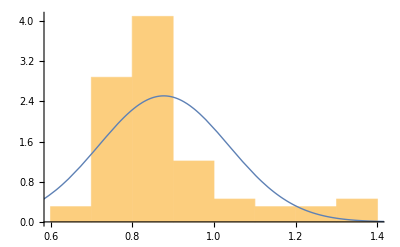

```mathematica
Show[Histogram[dataTreppeMitGeschw[All, "Geschwindigkeit"],10, "PDF"],Plot[PDF[NormalDistribution[geschwMean,geschwDeviation],x],{x,0,1.5},PlotStyle->Thick]]
```

## Quantileplot

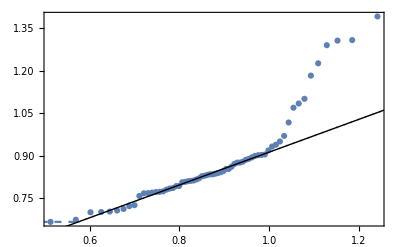

```mathematica
QuantilePlot[dataTreppeMitGeschw[All, "Geschwindigkeit"]]
```

## Distribution Fit Test

```mathematica
DistTestTreppe=DistributionFitTest[Array[dataTreppeMitGeschw[All, "Geschwindigkeit"], 66],Automatic,"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
DistTestTreppe["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 3.66723 | 6.20017×10^-7
Baringhaus-Henze | 4.53865 | 0.0000127914
Cramér-von Mises | 0.634851 | 0.
Jarque-Bera ALM | 45.2212 | 0.000864057
Mardia Combined | 45.2212 | 0.000864057
Mardia Kurtosis | 3.44345 | 0.000574336
Mardia Skewness | 26.5574 | 2.55817×10^-7
Pearson χ^2 | 25. | 0.00155456
Shapiro-Wilk | 0.835009 | 4.31299×10^-7

Der Distribution Fit Test ergibt, dass die Geschwindigkeiten NICHT normalverteilt sind. Laut dem Cramer-von Mises Test wird die 5% Hürde nicht überschritten.
Die Geschwindigkeiten Beim Raufgehen der Treppen sind nicht normalverteilt.

## Ausreißer entfernen

Es wurde festgestellt, dass die Geschwindigkeiten nicht normalverteilt sind. Es wird untersucht, ob die Ausreißer einen signifikanten Einfluss ausüben.

```mathematica
dataOhneAusreisser = dataTreppeMitGeschw[Select[#"Bemerkung"==""&], "Geschwindigkeit"]
```

Dataset[<>]

```mathematica
geschwNeuMean = Mean[dataOhneAusreisser]
```

0.814919

```mathematica
geschwNeuDeviation = StandardDeviation[dataOhneAusreisser]
```

0.0691465

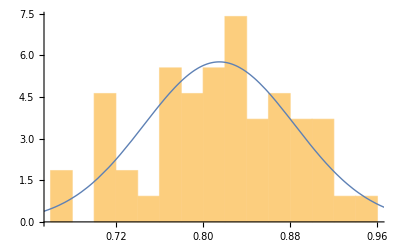

```mathematica
Show[Histogram[dataOhneAusreisser,10, "PDF"],Plot[PDF[NormalDistribution[geschwNeuMean,geschwNeuDeviation],x],{x,0,1},PlotStyle->Thick]]
```

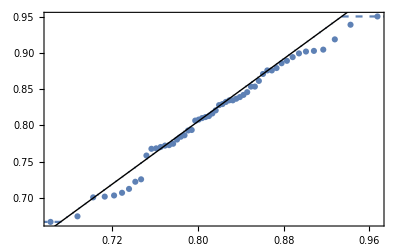

```mathematica
QuantilePlot[dataOhneAusreisser]
```

```mathematica
DistTestTreppeOhneAusreisser=DistributionFitTest[Array[dataOhneAusreisser, 54],Automatic,"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
DistTestTreppeOhneAusreisser["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 0.350758 | 0.476408
Baringhaus-Henze | 0.213705 | 0.524718
Cramér-von Mises | 0.0432779 | 0.623123
Jarque-Bera ALM | 1.31475 | 0.440072
Mardia Combined | 1.31475 | 0.440072
Mardia Kurtosis | -0.891517 | 0.372652
Mardia Skewness | 0.553342 | 0.456956
Pearson χ^2 | 10.8148 | 0.146903
Shapiro-Wilk | 0.977864 | 0.414303

Es ist festzustellen, dass die Geschwindigkeiten normalverteilt sind, wenn die Ausreißer nicht berücksichtigt werden. Für spätere betrachtung muss entschieden werden, ob diese Ausreisser in die Auswertung mit einfließen oder nicht.